# Red blood cell metabolism

```mathematica
<<Toolbox`
<<Toolbox`Style`
```

## Construction and parameterization of a MASS model

Construct a model of glycolysis.

```mathematica
glycolysis=constructModel[{Overscript[atp^c+glu^c⇌adp^c+g6p^c+h^c, vhk],Overscript[g6p^c⇌f6p^c, vpgi],Overscript[atp^c+f6p^c⇌adp^c+fdp^c+h^c, vpfk],Overscript[dhap^c⇌gap^c, vtpi],Overscript[fdp^c⇌dhap^c+gap^c, vald],Overscript[gap^c+nad^c+phos^c⇌h^c+nadh^c+pg13^c, vgapdh],Overscript[adp^c+pg13^c⇌atp^c+pg3^c, vpgk],Overscript[pg3^c⇌pg2^c, vpglm],Overscript[pg2^c⇌h2o^c+pep^c, veno],Overscript[adp^c+h^c+pep^c⇌atp^c+pyr^c, vpk],Overscript[h^c+nadh^c+pyr^c⇌lac^c+nad^c, vldh],(amp^c⇌∅)^vamp,Overscript[2 adp^c⇌amp^c+atp^c, vapk],(pyr^c⇌∅)^vpyr,(lac^c⇌∅)^vlac,Overscript[atp^c+h2o^c⇌adp^c+h^c+phos^c, vatp],Overscript[nadh^c⇌h^c+nad^c, vnadh],(∅⇌glu^c)^vgluin,(∅⇌amp^c)^vampin,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o},Ignore->{h^c,h2o^c},UnitChecking->True];
```

```mathematica
setInitialConditions[glycolysis,{glu^c->1. Millimole Liter^-1,g6p^c->0.0486 Millimole Liter^-1,f6p^c->0.0198 Millimole Liter^-1,fdp^c->0.0146 Millimole Liter^-1,dhap^c->0.16 Millimole Liter^-1,gap^c->0.00728 Millimole Liter^-1,pg13^c->0.000243 Millimole Liter^-1,pg3^c->0.0773 Millimole Liter^-1,pg2^c->0.0113 Millimole Liter^-1,pep^c->0.017 Millimole Liter^-1,pyr^c->0.060301 Millimole Liter^-1,lac^c->1.36 Millimole Liter^-1,nad^c->0.0589 Millimole Liter^-1,nadh^c->0.0301 Millimole Liter^-1,amp^c->0.08672812499999999 Millimole Liter^-1,adp^c->0.29 Millimole Liter^-1,atp^c->1.6 Millimole Liter^-1,phos^c->2.5 Millimole Liter^-1,h^c->0.00008997573444801929 Millimole Liter^-1,h2o^c->1. Millimole Liter^-1}]
```

```mathematica
setParameters[glycolysis,{Underscript[K, vhk]->850,Underscript[K, vpgi]->0.41,Underscript[K, vpfk]->310,Underscript[K, vtpi]->0.05714285714285714,Underscript[K, vald]->0.082 Millimole Liter^-1,Underscript[K, vgapdh]->0.0179 Liter Millimole^-1,Underscript[K, vpgk]->1800,Underscript[K, vpglm]->0.14705882352941177,Underscript[K, veno]->1.6949152542372883,Underscript[K, vpk]->363000,Underscript[K, vldh]->26300,Underscript[K, vamp]->∞,Underscript[K, vapk]->1.65,Underscript[K, vpyr]->1.,Underscript[K, vlac]->1.,Underscript[K, vatp]->∞ Millimole Liter^-1,Underscript[K, vnadh]->∞,Underscript[K, vgluin]->∞(*K_vgluin->1.1*),Underscript[K, vampin]->∞,Underscript[K, vh]->1.,Underscript[K, vh2o]->1.,pyr^Xt->0.06 Millimole Liter^-1,amp^Xt->Millimole Liter^-1,h^Xt->0.00006309573444801929 Millimole Liter^-1,h2o^Xt->Millimole Liter^-1,glu^Xt->Millimole Liter^-1,lac^Xt->Millimole Liter^-1,p["Volume","c"]->1 Liter}]
```

Calculate a set of steady-state fluxes.

```mathematica
basis=({
 {1, 0, 1},
 {1, 0, 0},
 {0, 1, 0}
}).NullSpace[glycolysis];
TableForm[basis.glycolysis["Fluxes"]]
```

v_vald+2 v_vatp+2 v_veno+2 v_vgapdh+v_vgluin+2 v_vh+v_vhk+2 v_vlac+2 v_vldh+v_vpfk+v_vpgi+2 v_vpgk+2 v_vpglm+2 v_vpk+v_vtpi
2 v_vh-v_vlac-v_vldh+v_vnadh+v_vpyr
v_vamp+v_vampin

```mathematica
solution={1.12,0.224,0.014}.basis;
steadyStateFluxes=#[[1]]->#[[2]]Millimole  Hour^-1&/@Thread[Rule[glycolysis["Fluxes"],solution]]
```

{v_vhk→1.12 Millimole Hour^-1,v_vpgi→1.12 Millimole Hour^-1,v_vpfk→1.12 Millimole Hour^-1,v_vtpi→1.12 Millimole Hour^-1,v_vald→1.12 Millimole Hour^-1,v_vgapdh→2.24 Millimole Hour^-1,v_vpgk→2.24 Millimole Hour^-1,v_vpglm→2.24 Millimole Hour^-1,v_veno→2.24 Millimole Hour^-1,v_vpk→2.24 Millimole Hour^-1,v_vldh→2.016 Millimole Hour^-1,v_vamp→0.014 Millimole Hour^-1,v_vapk→0. Millimole Hour^-1,v_vpyr→0.224 Millimole Hour^-1,v_vlac→2.016 Millimole Hour^-1,v_vatp→2.24 Millimole Hour^-1,v_vnadh→0.224 Millimole Hour^-1,v_vgluin→1.12 Millimole Hour^-1,v_vampin→0.014 Millimole Hour^-1,v_vh→2.688 Millimole Hour^-1,v_vh2o→0. Millimole Hour^-1}

```mathematica
updateInitialConditions[glycolysis,steadyStateFluxes];
```

```mathematica
perc=calcPERC[glycolysis]/.Undefined->100000;
updateParameters[glycolysis,perc];
```

calcPERC::atequilibrium: Reaction "vapk" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::atequilibrium: Reaction "vh2o" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Liter Hour^-1 Millimole^-1

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed: 100000 Hour^-1

### Simulate the model

```mathematica
{concSol,fluxSol}=simulate[glycolysis,{t,0,100}];
```

### Visualize the time-course concentration and flux profiles

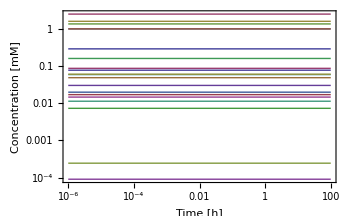

```mathematica
plotSimulation[concSol,FrameLabel->{"Time [h]","Concentration [mM]"}]
```

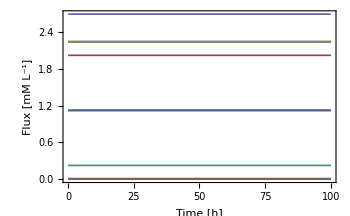

```mathematica
plotSimulation[fluxSol,PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mM L^-1]"}]
```

### Perturb the model and analyze the dynamic consequences

Simulate a glucose pulse at t=1.

```mathematica
{concSol,fluxSol}=simulate[glycolysis,{t,0.,1000},Events->{"Glucose pulse"->WhenEvent[t==1,m["glu","c"][t]->2Millimole Liter^-1]}];
```

Visualize the time-course profiles of concentrations, fluxes, and Atkins and Redox energy charges.

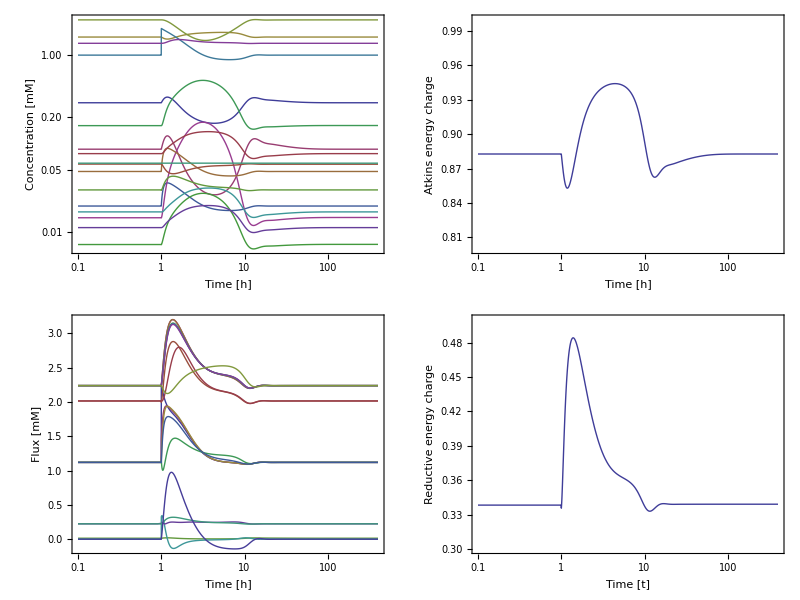

```mathematica
padding={{Scaled[0.035],Scaled[0.01]},{Automatic,Automatic}};
opts={ImagePadding->padding};
Grid[
{{plotSimulation[FilterRules[concSol,Except[{h^c,h2o^c,pg13^c}]],{t,0.1,400},FrameLabel->{"Time [h]","Concentration [mM]"},Sequence@@opts],plotSimulation[{"Atkins energy charge"->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c)}/.concSol,{t,0.1,400},PlotFunction->LogLinearPlot,PlotRange->{All,{0.8,1.}},FrameLabel->{"Time [h]","Atkins energy charge"},Sequence@@opts]},
{plotSimulation[FilterRules[fluxSol,Except[{Subscript[v, vh]}]],{t,0.1,400},FrameLabel->{"Time [h]","Flux [mM]"},PlotFunction->LogLinearPlot,Sequence@@opts],
plotSimulation[{"Redox charge"->nadh^c/(nad^c+nadh^c)}/.concSol,{t,0.1,400},FrameLabel->{"Time [t]","Reductive energy charge"},PlotFunction->LogLinearPlot,PlotRange->{All,{0.3,0.5}},Sequence@@opts]}}
]
AutoCollapse[]
```

Draw an animation of the fluxes on node maps.

```mathematica
nodeMapFrames=Table[Grid@Partition[Show[#,ImageSize->300]&/@filter[drawNodeMaps[glycolysis,Fluxes->Chop@stripUnits[fluxSol],Legend->False,PlotLabel->False],{h^c,adp^c,atp^c,amp^c,h2o^c,nad^c,nadh^c,pyr^c,dhap^c}][[All,2]],3],{t,1,15}];
```

```mathematica
ListAnimate[nodeMapFrames]
```

## Coupling pathways

### Combining individual pathway models

Load the glycolysis, pentose phosphate, nucleotide salvage pathways:

```mathematica
glycolysis=ExampleData[{"Toolbox","Glycolysis"}];
ppp=ExampleData[{"Toolbox","PentosePhosphatePathway"}];
salvage=ExampleData[{"Toolbox","NucleotideSalvagePathway"}];
hemoglobin=ExampleData[{"Toolbox","Hemoglobin"}];
```

Set operations like Intersection, Complement etc. can be applied to models. In this case we’ll use the Union function to merge the three pathways and get rid of redundant reactions. Models take precedence from left to right in terms of parameters, initial conditions, and other model attributes.

```mathematica
combi=Union[glycolysis,ppp,salvage,hemoglobin];
```

We can remove a few obsolete reaction using the deleteReactions function (remember that structural operations do not change the model in-place):

```mathematica
combi=deleteReactions[combi,{"EX_g6p_c","EX_f6p_c","EX_gap_c","EX_h_c","EX_h2o_c","EX_r5p_c","vamp","vampin","vatpgen"}];
```

The merged model contains 40 metabolites and 46 reactions:

```mathematica
combi//Dimensions
```

{48,53}

The merged model is not in a steady-state:

```mathematica
{concSol,fluxSol}=simulate[combi,{t,0,1*^6}];
```

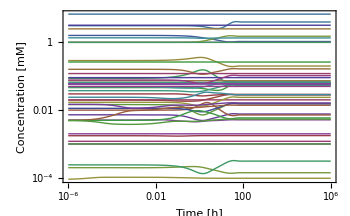

```mathematica
plotSimulation[concSol,FrameLabel->{"Time [h]","Concentration [mM]"}]
```

### Relaxation

We could set a new steady-state flux state and recalculate all PERCs etc. or we could just determine the steady-state the system relaxes to and use it as our new initial conditions for the merge model:

```mathematica
newSS=Flatten[{concSol,fluxSol}]/.t->1*^6;
combiRelaxed=combi;
updateInitialConditions[combiRelaxed,newSS];
```

The merged model with the new initial conditions is in a steady-state:

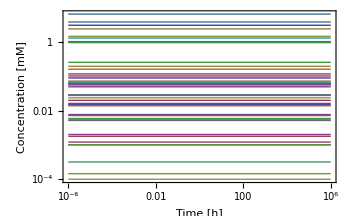

```mathematica
plotSimulation[simulate[combiRelaxed,{t,0,1*^6}][[1]],FrameLabel->{"Time [h]","Concentration [mM]"}]
```

```mathematica
{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.combi

{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.combiRelaxed
```

{E.C.→0.882772,Redox→0.338202,Redox2→0.99697}

{E.C.→0.876865,Redox→0.326867,Redox2→0.997853}

Comparing the initial conditions of the individual pathways with the newly obtained steady state reveals that fluxes and concentration are not dramatically different:

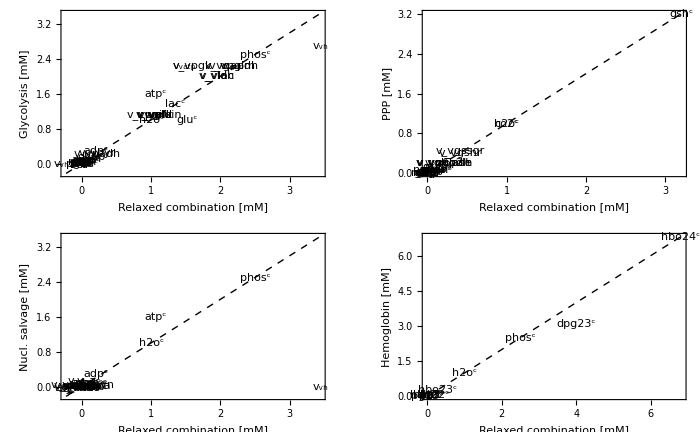

```mathematica
comparisonPlot=Show[Graphics[Text[#[[1]],#[[2]]]&/@#,Frame->True,##2,AspectRatio->1/GoldenRatio,PlotRange->All,ImagePadding->{{Scaled[0.15],Scaled[0.015]},{Automatic,Automatic}}],Graphics[{Dashed,Line[{{Min[#[[All,2]]],Min[#[[All,2]]]},{Max[#[[All,2]]],Max[#[[All,2]]]}}]}],BaseStyle->{FontFamily->"Helvetica",FontSize->12}]&;
GraphicsGrid[Partition[
{comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],glycolysis["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","Glycolysis [mM]"}],
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],ppp["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","PPP [mM]"}],
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],salvage["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","Nucl. salvage [mM]"}],
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],hemoglobin["InitialConditions"]]],FrameLabel->{"Relaxed combination [mM]","Hemoglobin [mM]"}]},2],ImageSize->350*2]
AutoCollapse[]
```

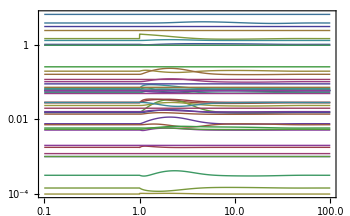

```mathematica
{concSol,fluxSol}=simulate[combiRelaxed,{t,.1,100},Events->{"Glucose pulse"->WhenEvent[t==1,glu^c[t]->2Millimole Liter^-1]}];
plotSimulation[concSol]
```

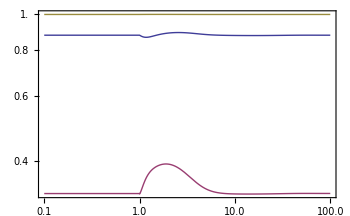

```mathematica
plotSimulation[{"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c),"Redox"->nadh^c/(nad^c+nadh^c),"Redox2"->nadph^c/(nadp^c+nadph^c)}/.concSol]
```

```mathematica
{concSolHb,fluxSolHb}=simulate[combiRelaxed,{t,0,.2},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4}];
```

```mathematica
o2Saturation={"r_OHb"->(25 (hbo2^c+2 hbo22^c+3 hbo23^c+4 hbo24^c))/(dhb^c+hb^c+hbo2^c+hbo22^c+hbo23^c+hbo24^c)};
```

```mathematica
plots={plotSimulation[o2Saturation/.concSolHb,PlotFunction->Plot,PlotRange->{All,{80,100}},FrameLabel->{"Time [h]","O_2 saturation [%]"}],plotSimulation[filter[fluxSolHb,{Subscript[v, vo2]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Legend->{Bottom,Right}],plotSimulation[FilterRules[fluxSolHb,{Subscript[v, vgapdh],Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}],
plotSimulation[FilterRules[fluxSolHb,{Subscript[v, vdpgm],Subscript[v, vdpgase]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]};
```

```mathematica
SlideView[plots]
```

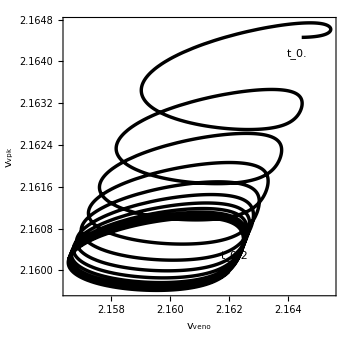

```mathematica
plotPhasePortrait[filter[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk]}]]
```

## Adding regulation

### Build and parameterize elementary reaction enzyme module for Phosphofruktokinase (PFK)

#### Construct the module

Write out the catalytic mechanism using textual input:

```mathematica
catalyticBranch={
"E_PFK[c]&atp + f6p[c] <=> E_PFK[c]&atp&f6p",
"E_PFK[c] + atp[c] <=> E_PFK[c]&atp",
"E_PFK[c]&atp&f6p -> E_PFK[c] + fdp[c] + adp[c] + h[c]"
};
```

Construct the enzyme module

```mathematica
module=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{amp^c},ActivationSites->4,Inhibitors->{atp^c},InhibitionSites->4];
```

The figure from the book is easier to grasp:

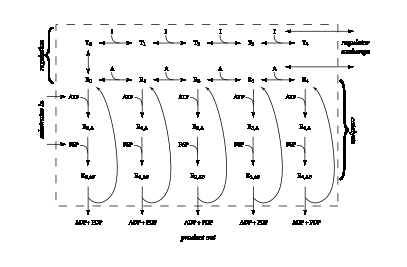

Don’t distinguish between the elementary rate-constants of the four different catalytic branches:

```mathematica
updateCustomRateLaws[module,Thread[(getID/@module["Fluxes"])->unifyRateConstants[module["Rates"]]]]
```

Include the inverses of the dissociation constants (from the book) as equilibrium constants in the model:

```mathematica
updateParameters[module,{Underscript[K, PFK1]->1/0.068,Underscript[K, PFK2]->1/0.1,Underscript[K, PFK_Activation_amp]->1/0.033,Underscript[K, PFK_Inhibition_atp]->1/0.1(*Increased by factor of 10*),Underscript[K, PFK_TransitionStep]->0.0011}]
```

#### Assumptions

The steady-state flux through the PFK sub network is given by

```mathematica
vpfkEq=p["v","pfk"]==rateconst["PFK3",True](Total[Cases[module["Species"],e_enzyme/;getCatalytic[e]==={m["atp","c"],m["f6p","c"]}]])
```

v_pfk==((PFK^c&atp^c&f6p^c)_^+(PFK^c&atp^c&f6p^c)_^(amp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c)) k_PFK3^⟶

Enumerate all enzyme forms in the module:

```mathematica
enzForms=Cases[module["Species"],_enzyme]//Union
Length@enzForms
```

{(PFK^c)_^,(PFK^c)_^(amp^c),(PFK^c)_^(amp^camp^c),(PFK^c)_^(amp^camp^camp^c),(PFK^c)_^(amp^camp^camp^camp^c),(PFK^c&atp^c)_^,(PFK^c&atp^c)_^(amp^c),(PFK^c&atp^c)_^(amp^camp^c),(PFK^c&atp^c)_^(amp^camp^camp^c),(PFK^c&atp^c)_^(amp^camp^camp^camp^c),(PFK^c&atp^c&f6p^c)_^,(PFK^c&atp^c&f6p^c)_^(amp^c),(PFK^c&atp^c&f6p^c)_^(amp^camp^c),(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c),(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c),(PFK_T^c)_^,(PFK_T^c)_(atp^c)^,(PFK_T^c)_(atp^catp^c)^,(PFK_T^c)_(atp^catp^catp^c)^,(PFK_T^c)_(atp^catp^catp^catp^c)^}

20

#### Solve the steady-state equations

Extract the ODE for the enzyme forms and set their time derivatives to zero to generate the steady-state equations:

```mathematica
enzPos=Flatten[Position[module["Species"],_enzyme]];
ssEq=stripTime[module["ODE"][[enzPos]]/._'[t]->0];
SlideView[ssEq]
```

Solve for the enzyme forms using the overall reaction and steady-state equations (anonymize speeds up the calculations by translating all enzyme, metabolite, constants etc. temporarily into anonymous variables); simplify the solution afterwards.

```mathematica
sol=anonymize[Solve[Join[ssEq,{vpfkEq}],enzForms]];
sol=Simplify[sol][[1]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["PFK_ss_sol.m",sol];
sol=Import["PFK_ss_sol.m"];
```

```mathematica
SlideView[Simplify[keq2k@sol]]
```

#### The steady-state solution

In order to prepare Table 14.3 we need to obtain the four different 
categories of enzyme forms:

```mathematica
ri0=Cases[enzForms,e_enzyme/;getCatalytic[e]=={}&&getInhibitors[e]=={}&&getID[e]=="PFK"];
riA=Cases[enzForms,e_enzyme/;getCatalytic[e]=={atp^c}&&getInhibitors[e]=={}&&getID[e]=="PFK"];
riAF=Cases[enzForms,e_enzyme/;getCatalytic[e]=={atp^c,f6p^c}&&getInhibitors[e]=={}&&getID[e]=="PFK"];
tforms=Cases[enzForms,e_enzyme/;getID[e]=="PFK_T"];
```

```mathematica
SlideView[{ri0,riA,riAF,tforms}]
```

Now we can generate Table 14.3:

```mathematica
tab14$3=Simplify@Grid[Join[{{"i","R_(i, 0)","R_(i, 0)/R_(i, 0)","R_(i, A)/R_(i, 0)","R_(i, AF)/R_(i, 0)","R_(i, 0)/R_(1, 0)","T_i/T_0"}},Transpose[{{0,1,2,3,4},
ri0,
ri0/ri0,
ri0/riA,
ri0/riAF,
ri0/ri0[[1]],
tforms/tforms[[1]]
}/.keq2k@sol]],Dividers->{{False,True},{False,True}}]
```

i | R_(i, 0) | R_(i, 0)/R_(i, 0) | R_(i, A)/R_(i, 0) | R_(i, AF)/R_(i, 0) | R_(i, 0)/R_(1, 0) | T_i/T_0
0 | (v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟵)^4)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | 1 | 1
1 | (4 amp^c v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟵)^3 k_PFK_Activation_amp^⟶)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | (4 amp^c k_PFK_Activation_amp^⟶)/k_PFK_Activation_amp^⟵ | (4 atp^c k_PFK_Inhibition_atp^⟶)/k_PFK_Inhibition_atp^⟵
2 | (6 (amp^c)^2 v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟵)^2 (k_PFK_Activation_amp^⟶)^2)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | (6 (amp^c)^2 (k_PFK_Activation_amp^⟶)^2)/((k_PFK_Activation_amp^⟵)^2) | (6 (atp^c)^2 (k_PFK_Inhibition_atp^⟶)^2)/((k_PFK_Inhibition_atp^⟵)^2)
3 | (4 (amp^c)^3 v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) k_PFK_Activation_amp^⟵ (k_PFK_Activation_amp^⟶)^3)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | (4 (amp^c)^3 (k_PFK_Activation_amp^⟶)^3)/((k_PFK_Activation_amp^⟵)^3) | (4 (atp^c)^3 (k_PFK_Inhibition_atp^⟶)^3)/((k_PFK_Inhibition_atp^⟵)^3)
4 | ((amp^c)^4 v_pfk (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶)) (k_PFK_Activation_amp^⟶)^4)/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶ k_PFK3^⟶ (k_PFK_Activation_amp^⟵+amp^c k_PFK_Activation_amp^⟶)^4) | 1 | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c k_PFK1^⟶ (k_PFK2^⟵+k_PFK3^⟶)) | (f6p^c k_PFK2^⟶ k_PFK3^⟶+k_PFK1^⟵ (k_PFK2^⟵+k_PFK3^⟶))/(atp^c f6p^c k_PFK1^⟶ k_PFK2^⟶) | ((amp^c)^4 (k_PFK_Activation_amp^⟶)^4)/((k_PFK_Activation_amp^⟵)^4) | ((atp^c)^4 (k_PFK_Inhibition_atp^⟶)^4)/((k_PFK_Inhibition_atp^⟵)^4)

Make it look similar to the table in the book:

```mathematica
tab14$3/.{Subscript[k, PFK3]^⟶->Subscript[k, PFK]^⟶,Subscript[k, PFK1]^⟶->Subscript[k, A]^⟶,Subscript[k, PFK1]^⟵->Subscript[k, A]^⟵,Subscript[k, PFK2]^⟶->Subscript[k, F]^⟶,Subscript[k, PFK2]^⟵->Subscript[k, F]^⟵,Subscript[k, PFK_Activation_amp]^⟶->Subscript[k, a]^⟶,Subscript[k, PFK_Activation_amp]^⟵->Subscript[k, a]^⟵,Subscript[k, PFK_Inhibition_atp]^⟶->Subscript[k, i]^⟶,Subscript[k, PFK_Inhibition_atp]^⟵->Subscript[k, i]^⟵}
```

i | R_(i, 0) | R_(i, 0)/R_(i, 0) | R_(i, A)/R_(i, 0) | R_(i, AF)/R_(i, 0) | R_(i, 0)/R_(1, 0) | T_i/T_0
0 | (v_pfk (k_a^⟵)^4 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | 1 | 1
1 | (4 amp^c v_pfk (k_a^⟵)^3 k_a^⟶ (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | (4 amp^c k_a^⟶)/k_a^⟵ | (4 atp^c k_i^⟶)/k_i^⟵
2 | (6 (amp^c)^2 v_pfk (k_a^⟵)^2 (k_a^⟶)^2 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | (6 (amp^c)^2 (k_a^⟶)^2)/((k_a^⟵)^2) | (6 (atp^c)^2 (k_i^⟶)^2)/((k_i^⟵)^2)
3 | (4 (amp^c)^3 v_pfk k_a^⟵ (k_a^⟶)^3 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | (4 (amp^c)^3 (k_a^⟶)^3)/((k_a^⟵)^3) | (4 (atp^c)^3 (k_i^⟶)^3)/((k_i^⟵)^3)
4 | ((amp^c)^4 v_pfk (k_a^⟶)^4 (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶)))/(atp^c f6p^c (k_a^⟵+amp^c k_a^⟶)^4 k_A^⟶ k_F^⟶ k_PFK^⟶) | 1 | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c k_A^⟶ (k_F^⟵+k_PFK^⟶)) | (f6p^c k_F^⟶ k_PFK^⟶+k_A^⟵ (k_F^⟵+k_PFK^⟶))/(atp^c f6p^c k_A^⟶ k_F^⟶) | ((amp^c)^4 (k_a^⟶)^4)/((k_a^⟵)^4) | ((atp^c)^4 (k_i^⟶)^4)/((k_i^⟵)^4)

#### Numerical values

The conserved enzyme pool

```mathematica
pfktot=p["PFKtot"]==Total[enzForms]
```

PFKtot_Global==(PFK^c)_^+(PFK^c)_^(amp^c)+(PFK^c)_^(amp^camp^c)+(PFK^c)_^(amp^camp^camp^c)+(PFK^c)_^(amp^camp^camp^camp^c)+(PFK^c&atp^c)_^+(PFK^c&atp^c)_^(amp^c)+(PFK^c&atp^c)_^(amp^camp^c)+(PFK^c&atp^c)_^(amp^camp^camp^c)+(PFK^c&atp^c)_^(amp^camp^camp^camp^c)+(PFK^c&atp^c&f6p^c)_^+(PFK^c&atp^c&f6p^c)_^(amp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c)+(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c)+(PFK_T^c)_^+(PFK_T^c)_(atp^c)^+(PFK_T^c)_(atp^catp^c)^+(PFK_T^c)_(atp^catp^catp^c)^+(PFK_T^c)_(atp^catp^catp^catp^c)^

Substitute all know parameters and the steady-state solutions

```mathematica
pfktot=Simplify[pfktot/.sol/.stripUnits@combiRelaxed["InitialConditions"]/.Underscript[v, pfk]->1.12/.module["Parameters"]]
```

PFKtot_Global==1.35752/k_PFK1^⟶+43.2559/k_PFK2^⟶+5.44559/k_PFK3^⟶

Solver for k_PFK3^⟶

```mathematica
kpfkSol=Quiet[Solve[pfktot,Subscript[k, PFK3]^⟶][[1]],Solve::ratnz]
```

{k_PFK3^⟶→(1.93006×10^14 k_PFK1^⟶ k_PFK2^⟶)/(-1.5331×10^15 k_PFK1^⟶-4.81142×10^13 k_PFK2^⟶+3.54426×10^13 PFKtot_Global k_PFK1^⟶ k_PFK2^⟶)}

Plot the feasible parameters space and color code the fraction of T-form enzymes

```mathematica
tFraction=Simplify[Total[tforms]/Total[enzForms]/.sol]/.module["Parameters"]/.stripUnits[glycolysis["InitialConditions"]];
tFractionFunction=tFraction/.{Subscript[k, PFK1]^⟶->#1,Subscript[k, PFK2]^⟶->#2,Subscript[k, PFK3]^⟶->#3}&;
tFractionFunctionLog=tFraction/.{Subscript[k, PFK1]^⟶->10^#1,Subscript[k, PFK2]^⟶->10^#2,Subscript[k, PFK3]^⟶->10^#3}&;
tFractionColorFunction=ColorData["DarkBand"][tFraction/.{Subscript[k, PFK1]^⟶->#1,Subscript[k, PFK2]^⟶->#2,Subscript[k, PFK3]^⟶->#3}]&;
tFractionColorFunctionLog=ColorData["DarkBands"][tFraction/.{Subscript[k, PFK1]^⟶->10^#1,Subscript[k, PFK2]^⟶->10^#2,Subscript[k, PFK3]^⟶->10^#3}]&;
paramSpacePlot=Legended[Plot3D[Evaluate[Log[10,Subscript[k, PFK3]^⟶/.kpfkSol/.{Subscript[k, PFK1]^⟶->10^kap,Subscript[k, PFK2]^⟶->10^kfp,Underscript[PFKtot, Global]->33*^-6}]],{kap,1,10},{kfp,1,10},ColorFunction->tFractionColorFunctionLog,ColorFunctionScaling->False,PlotPoints->100,PlotRange->{Full,Full,{5,9}},AxesLabel->{"k_A^+ [log_10]","k_F^+ [log_10]","k_PFK^+ [log_10]"},ImageSize->500,ViewPoint->{Pi,Pi/2,2}],BarLegend[{"DarkBands",{0,1}},LegendLayout->"Column",LegendLabel->"T/PFK_tot",LabelStyle->{FontFamily->"Helvetica"}]]
AutoCollapse[]
```

-Graphics3D-

The enzyme is inhibited between 10–15% under physiological conditions (Ponce et al. Biochimica et Biophysica Acta 1971 250(1):63-74). The parameter values indicated in green correspond to a 10–15% fraction of T-forms.

```mathematica
stripePlot=Legended[Plot3D[Evaluate[Log[10,Subscript[k, PFK3]^⟶/.kpfkSol/.{Subscript[k, PFK1]^⟶->10^kap,Subscript[k, PFK2]^⟶->10^kfp,Underscript[PFKtot, Global]->33*^-6}]],{kap,0,12},{kfp,0,12},ColorFunction->(If[.1<tFractionFunctionLog[##]<.15,Green,LightGray]&),ColorFunctionScaling->False,AxesLabel->{"k_A^+ [log_10]","k_F^+ [log_10]","k_PFK^+ [log_10]"},PlotPoints->100,PlotRange->{Full,Full,{5,9}},ImageSize->500,ViewPoint->{Pi,Pi/2,2}],SwatchLegend[{Green},{"10–15% T-fraction"}]]
AutoCollapse[]
```

-Graphics3D-

Choose a feasible parameter combination

```mathematica
finalParamChoice={Subscript[k, PFK1]^⟶->116686.,Subscript[k, PFK2]^⟶->8.259528*^6,Subscript[k, PFK3]^⟶->432308.4041452617};
```

```mathematica
Show[stripePlot,Graphics3D[{PointSize[.05],Red,Point[#]}&@(Log[10,finalParamChoice/.r_Rule:>r[[2]]])],PlotRange->All]
AutoCollapse[]
```

-Graphics3D-

Parameterize the final PFK module and make it ready for integration

```mathematica
finalPFK=module;
updateParameters[finalPFK,finalParamChoice]
(*Add fast activation and inhibition rate-constants*)
updateParameters[finalPFK,{Subscript[k, PFK_Activation_amp]^⟶->1000000,Subscript[k, PFK_Inhibition_atp]^⟶->1000000,Subscript[k, PFK_TransitionStep]^⟶->1000000^2}]
(*updateParameters[finalPFK,{Subscript[k, PFK_Activation_amp]^⟶->10000,Subscript[k, PFK_Inhibition_atp]^⟶->10000,Subscript[k, PFK_TransitionStep]^⟶->10000^2}]*)
```

Calculate the numerical steady-state concentrations for the different enzyme forms:

```mathematica
enzFormConc=sol/.{parameter["v","pfk"]->1.12}/.stripUnits[finalPFK["Parameters"]]/.stripUnits[combiRelaxed["InitialConditions"]]
Total[enzFormConc[[All,2]]]
```

{(PFK^c)_^→1.42442×10^-7,(PFK^c)_^(amp^c)→1.0788×10^-6,(PFK^c)_^(amp^camp^c)→3.06389×10^-6,(PFK^c)_^(amp^camp^camp^c)→3.86745×10^-6,(PFK^c)_^(amp^camp^camp^camp^c)→1.83065×10^-6,(PFK^c&atp^c)_^→2.00927×10^-7,(PFK^c&atp^c)_^(amp^c)→1.52174×10^-6,(PFK^c&atp^c)_^(amp^camp^c)→4.32189×10^-6,(PFK^c&atp^c)_^(amp^camp^camp^c)→5.45537×10^-6,(PFK^c&atp^c)_^(amp^camp^camp^camp^c)→2.5823×10^-6,(PFK^c&atp^c&f6p^c)_^→3.69651×10^-8,(PFK^c&atp^c&f6p^c)_^(amp^c)→2.79959×10^-7,(PFK^c&atp^c&f6p^c)_^(amp^camp^c)→7.95109×10^-7,(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^c)→1.00364×10^-6,(PFK^c&atp^c&f6p^c)_^(amp^camp^camp^camp^c)→4.75072×10^-7,(PFK_T^c)_^→1.56687×10^-10,(PFK_T^c)_(atp^c)^→6.62704×10^-9,(PFK_T^c)_(atp^catp^c)^→1.05109×10^-7,(PFK_T^c)_(atp^catp^catp^c)^→7.40928×10^-7,(PFK_T^c)_(atp^catp^catp^catp^c)^→1.95859×10^-6}

0.0000294676

Include the enzyme concentrations in the inital conditions of the module

```mathematica
updateInitialConditions[finalPFK,enzFormConc]
```

### Integrate the PFK module into the RBC model

Integrate the parametrized PFK module with the glycolytic pathway.

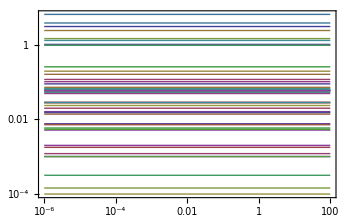

```mathematica
plotSimulation@simulate[combiRelaxed,{t,0,100}][[1]]
```

```mathematica
combiPFK=Union[deleteReactions[combiRelaxed,{"vpfk"}],finalPFK];
```

The system is initially in a steady-state.

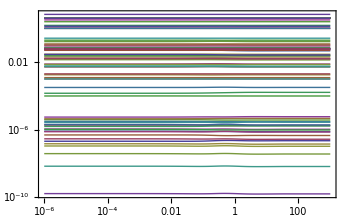

```mathematica
{concSol,fluxSol}=simulate[combiPFK,{t,0,1000}];
plotSimulation[concSol]
```

```mathematica
{concSolHb,fluxSolHb}=simulate[combiPFK,{t,0,0.5},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->2]},MaxSteps->∞];
```

```mathematica
SlideView[{plotSimulation[o2Saturation/.concSolHb,PlotFunction->Plot,PlotRange->{All,{80,100}},FrameLabel->{"Time [h]","O_2 saturation [%]"},Tooltipped->False],plotSimulation[filter[fluxSolHb,{Subscript[v, vo2]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Legend->{Bottom,Right},Tooltipped->False],plotSimulation[FilterRules[fluxSolHb,{Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Tooltipped->False],
plotSimulation[FilterRules[fluxSolHb,{Subscript[v, vdpgm],Subscript[v, vdpgase]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"},Tooltipped->False]}]
```

Compare the dynamic responses of glycolysis to a glucose pulse with and without the PFK sub-network.

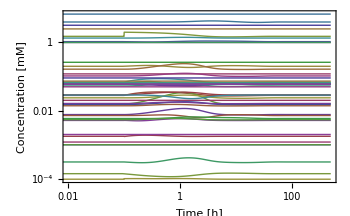

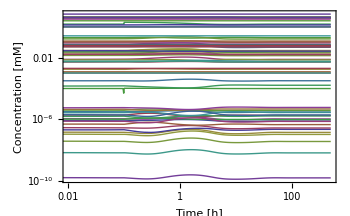

```mathematica
{perturbedConcSol1,perturbedFluxSol1}=simulate[combiRelaxed,{t,0,500},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->2.]}];
plotSimulation[perturbedConcSol1,PlotRange->{{0.01,All},All},FrameLabel->{"Time [h]","Concentration [mM]"}]
{perturbedConcSol2,perturbedFluxSol2}=simulate[combiPFK,{t,0,500},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->2.]}];
plotSimulation[perturbedConcSol2,PlotRange->{{0.01,All},All},FrameLabel->{"Time [h]","Concentration [mM]"}]
```

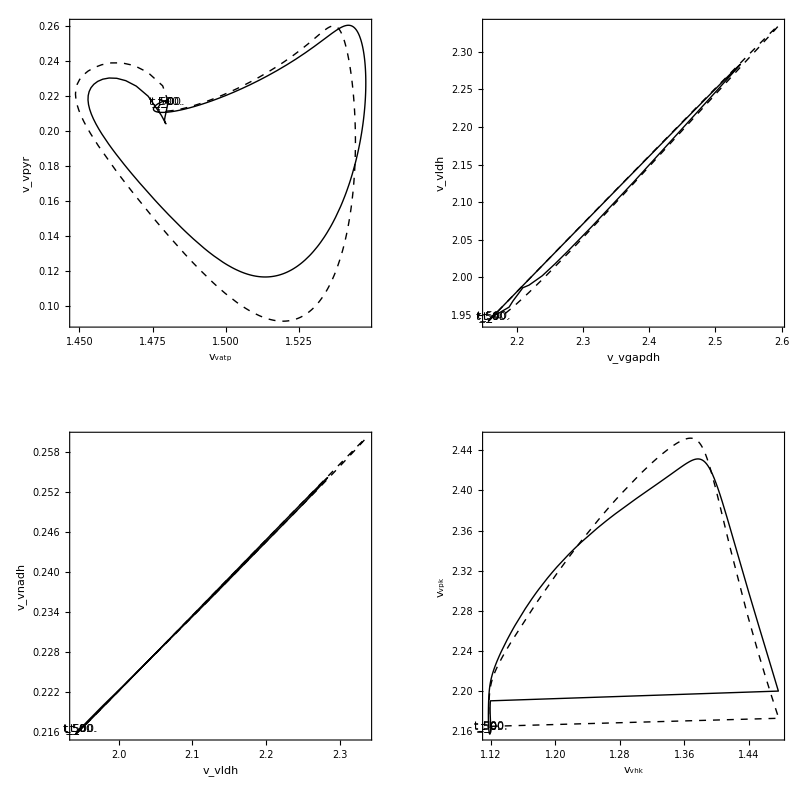

```mathematica
pairwisePlots=Table[
filteredSol={filter[perturbedFluxSol1,cmb],filter[perturbedFluxSol2,cmb]};
plotPhasePortrait[filteredSol,PlotStyle->{Directive[Black,Dashed],Directive[Black]},PlotPoints->500,FrameLabel->filteredSol[[1,All,1]]],{cmb,{{Subscript[v, vatp],Subscript[v, vpyr]},{Subscript[v, vgapdh],Subscript[v, vldh]},{Subscript[v, vldh],Subscript[v, vnadh]},{Subscript[v, vhk],Subscript[v, vpk]}}}];
Legended[GraphicsGrid[Partition[pairwisePlots,2],ImageSize->800],LineLegend[{Black,Directive[Black,Dashed]},{"Regulated","Unregulated"}]]
```

```mathematica
keyRatios={"r_R"->Total[Cases[combiPFK["Species"],e_enzyme/;getID[e]≠"PFK_T"]]/Total[Cases[combiPFK["Species"],e_enzyme]],
"E.C."->(adp^c/2+atp^c)/(adp^c+amp^c+atp^c)
};
```

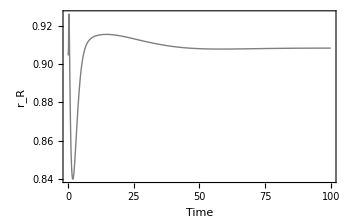

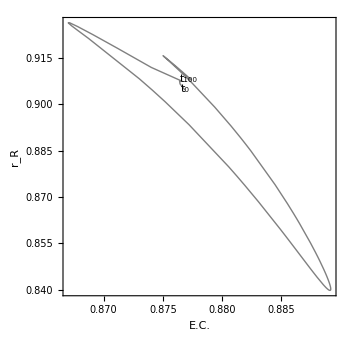

```mathematica
plotSimulation[filter[keyRatios,{"r_R"}]/.perturbedConcSol2,{t,0,100},PlotFunction->Plot,FrameLabel->{"Time","r_R"},PlotStyle->Gray]
plotPhasePortrait[filter[keyRatios,{"E.C.","r_R"}]/.perturbedConcSol2,{t,0,100},PlotStyle->Gray]
```

```mathematica
m["glu","c"]/.combiRelaxed
```

1.51318 Millimole Liter^-1

```mathematica
Module[{concSol},
Manipulate[
concSol=simulate[combiPFK,{t,0,100},Events->{"pulse"->WhenEvent[t==.1,glu^c[t]->glu]},Method->Automatic,PrecisionGoal->23][[1]];
GraphicsRow[{plotSimulation[filter[keyRatios,{"r_R"}]/.concSol,{t,0,100},PlotFunction->Plot,FrameLabel->{"Time","r_R"},Tooltipped->False,PlotRange->{All,{0.5,1.1}},PlotStyle->Black],
plotPhasePortrait[filter[keyRatios,{"E.C.","r_R"}]/.concSol,{t,0,100},PlotStyle->Gray,PlotRange->{{0.8,1},{0.65,1}}]}],{{glu,stripUnits[m["glu","c"]/.combiRelaxed],"Glucose conc."},.1,4}]]
(*AutoCollapse[]*)
```